```mathematica
■Analisis MAV
```

MAV ■Analisis

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{NotebookDirectory[],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{NotebookDirectory[],"EconomicComputations.wl"}]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
```

## Cargar base de datos

```mathematica
path = FileNameJoin[{NotebookDirectory[],"DJI_DAX_MXX_NIKKEI_dataset.mx"}];
database = Import[path];
database[[All,"Name"]] = {"DJIA","DAX","IPC","Nikkei 225"};
```

## Fechas percentuales

```mathematica
DaysInYear[year_] := First[DateDifference[{year, 1, 1}, {year, 12, 31}]] + 1;

YearPercentual[date_] := N[QuantityMagnitude[DateDifference[DateObject[{date["Year"], 1, 1}], date]] / DaysInYear[date["Year"]]] + date["Year"];

DateFromYearPercentual[yearPercentual_] := Block[{year, daysEllapsed, date},
	year = IntegerPart[yearPercentual];
	daysEllapsed = IntegerPart[(yearPercentual - year) * DaysInYear[year]];
	date = DatePlus[DateObject[{year, 1, 1}], daysEllapsed];
	Return[date];
];
```

```mathematica
Ventana[market_,dias_]:=MovingAverage[MapAt[YearPercentual, database[[market]]["DatedPrices"], {All,1}],dias];
```

rVentana arroja las fechas percentuales con los precios

```mathematica
rVentana = Ventana[1, 50];
```

DateFromYearPercentual cambia el formato de fecha de percentual a formato de fecha de mathematica

MAVDates devuelve las fechas en formato de fecha de mathematica

```mathematica
MAVDates = Map[DateFromYearPercentual[#] &, rVentana[[All, 1]]];
```

Se asignan a cada una de las fechas los precios. Fecha y precio será arrojada por MAVResult

```mathematica
MAVPrices = rVentana[[All, 2]];
MAVResult = Transpose[{MAVDates, MAVPrices}]
```

{{Day: Mon 16 Dec 1991,1597.36},{Day: Wed 18 Dec 1991,1598.91},{Day: Thu 19 Dec 1991,1600.39},6411,{Day: Wed 26 Apr 2017,12405.6},{Day: Thu 27 Apr 2017,12422.9},{Day: Sat 29 Apr 2017,12438.6}}
 |  |  |  |

Pero MAVResult es lo mismo que MAVDatePrice

```mathematica
MAVDatePrice = Transpose[{MAVDates, MAVPrices}];
ReturnLogs = MAVDatePrice[[All, 2]] // Returns;
DatesLogReturn = Drop[MAVDatePrice[[All, 1]], -1];
MAVReturn = Transpose[{DatesLogReturn, ReturnLogs}];
```

```mathematica
cuartiles = Quantile[MAVReturn[[All, 2]], {1/4, 1/2, 3/4}]
```

{-0.000556771,0.000587268,0.00151629}

```mathematica
MAVReturn
```

{{Day: Mon 16 Dec 1991,0.000968629},{Day: Wed 18 Dec 1991,0.000926452},{Day: Thu 19 Dec 1991,0.00063964},6410,{Day: Mon 24 Apr 2017,0.000987167},{Day: Wed 26 Apr 2017,0.00138681},{Day: Thu 27 Apr 2017,0.00126461}}
 |  |  |  |

Calcular sigma, mu , aquí, del resultado de los retornos de MAV

De los retornos de los datos reales, se obtiene μ y σ , y son utilizados para simular retornos por medio de un caminante aleatorio.

```mathematica
MeanReturns=Mean[MAVReturn[[All,2]]];
stdReturns=StandardDeviation[MAVReturn[[All,2]]];
randomV= RandomVariate[NormalDistribution[MeanReturns,stdReturns],Length[MAVReturn[[All,2]]]];

(*BuscarPrecio[datedPrices_,date_]:=FirstCase[datedPrices,{date,p_}:>p];
(*La siguiente linea de codigo nos da todas las fechas en que se tuvo minima entropia y su precio*)
Rastreador = Map[{#,BuscarPrecio[database[[market]]["DatedPrices"],#]}&,MercadoNoGaussiano[[All,1]]]*)
```

En esta parte se estandarizan los retornos, tanto reales, como lo simulados.

```mathematica
returnRealEstandarizado=Standardize[MAVReturn[[All,2]]];
```

```mathematica
returnSimuladosEstandarizados=Standardize[randomV];
```

```mathematica
Qreal=Quantile[returnRealEstandarizado,{1/4,1/2,3/4}];
Qsimula=Quantile[returnSimuladosEstandarizados,{1/4,1/2,3/4}];
```

```mathematica
intervaloReales=Partition[Join[{-∞},Qreal,{∞}],2,1];
intervaloSimulados=Partition[Join[{-∞},Qsimula,{∞}],2,1];
reglas[intervalo_]:=MapThread[(x_/;IntervalMemberQ[Interval[#1],x])->#2&,{intervalo,Range[4]}];
intervaloRDiscretizado=reglas[intervaloReales];
intervaloSDiscre=reglas[intervaloSimulados];
```

En la siguiente linea se obtienen los retornos discretizados

```mathematica
returnsDiscretosReales=returnRealEstandarizado/.intervaloRDiscretizado;
```

```mathematica
returnDiscretSimulados=returnSimuladosEstandarizados/.intervaloSDiscre;
```

Se acomoda fecha y valor de retorno discretizado, tanto para el real como para el simulado.

```mathematica
fechaReal=Drop[database[[1]]["Dates"],-50];
```

A continuacion viene fecha y dato para los valores del mercado real

```mathematica
FechaRetornoReal=Transpose[{fechaReal,returnsDiscretosReales}];
```

Lo mismo se hace para los datos simulados

```mathematica
FechaRetornoSimulado=Transpose[{fechaReal,returnDiscretSimulados}];
```

### Calculando entropías

Se ocupa una partición para cada uno, una particion para los retornos reales  y una partición para los simulados

```mathematica
particionRetReal[dias_]:=Partition[FechaRetornoReal,dias,1];
particionRetornoSimulados[dias_]:=Partition[FechaRetornoSimulado,dias,1];
```

### Entropia de los retornos reales

```mathematica
Sreal=Map[{Last[#[[All,1]]],N[Entropy[#[[All,2]]]]}&,particionRetReal[50]];
```

```mathematica
Entropia de los retornos simulados
```

de Entropia los retornos simulados

```mathematica
SSimulada=Map[{Last[#[[All,1]]],N[Entropy[#[[All,2]]]]}&,particionRetornoSimulados[50]];
```

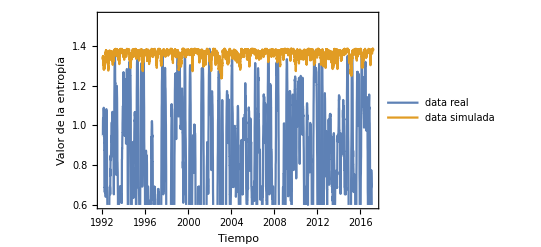

```mathematica
DateListPlot[{Sreal,SSimulada},PlotRange->{0.6,1.55},Frame->True,FrameLabel->{{"Valor de la entropía","2017"},{"Tiempo","Entropía de retornos reales y simulados"}},PlotLegends->{"data real", "data simulada"}]
```

```mathematica
Min[Sreal]
Max[Sreal]
```

Min::nord2: Comparison of DateObject[{1992,1,24},Day,Gregorian,-6.] and ∞ is invalid.

Min[0.,Day: Fri 24 Jan 1992]

Max::nord2: Comparison of DateObject[{2017,3,22},Day,Gregorian,-6.] and 1.38549 is invalid.

Max[1.38549,Day: Wed 22 Mar 2017]

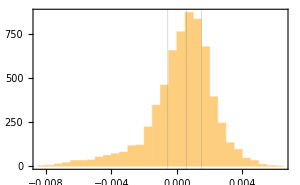

```mathematica
a=Histogram[MAVReturn[[All,2]],GridLines->{cuartiles,{}},PlotRange-> All,Frame-> True]
```

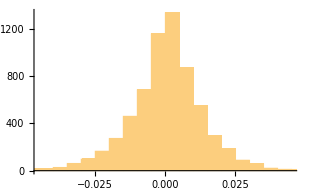

```mathematica
b=Histogram[database[[1]]["Returns"]]
```

```mathematica
intervalos=Partition[Join[{-∞},cuartiles,{∞}],2,1]
```

{{-∞,-0.000556771},{-0.000556771,0.000587268},{0.000587268,0.00151629},{0.00151629,∞}}

```mathematica
discreteStates=Range[Length[intervalos]];
reglas=MapThread[(x_/;IntervalMemberQ[Interval[#1],x])->#2&,{intervalos,discreteStates}];

resultado=MAVReturn[[All,2]]/.reglas;
```

```mathematica
discretoConFechas=Transpose[{MAVReturn[[All,1]],resultado}]
```

{{Day: Mon 16 Dec 1991,3},{Day: Wed 18 Dec 1991,3},{Day: Thu 19 Dec 1991,3},{Day: Sat 21 Dec 1991,3},{Day: Mon 23 Dec 1991,3},6406,{Day: Fri 21 Apr 2017,3},{Day: Sun 23 Apr 2017,3},{Day: Mon 24 Apr 2017,3},{Day: Wed 26 Apr 2017,3},{Day: Thu 27 Apr 2017,3}}
 |  |  |  |

```mathematica
Length[discretoConFechas]
```

6416

```mathematica
window=50;
```

```mathematica
parts=Partition[discretoConFechas,window,1];
resultado=Map[{Last[#[[All,1]]],N[Entropy[#[[All,2]]]]}&,parts];
```

```mathematica
i=1
```

1

```mathematica
Last[resultado]
```

{Day: Thu 27 Apr 2017,0.265158}

```mathematica
parts[[i]][[All,2]]
```

{3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,3,4,3,4,4,4,3,3,3,2,3,2,2,2,2,3,3}

```mathematica
For[i=1,i<6367,i++,Print[N[Entropy[parts[[i]][[All,2]]]]]];
```

0.948693

0.948693

0.948693

0.976895

1.00084

1.02096

1.03758

1.03758

1.03758

«7 more identical outputs»

1.03953

1.05492

1.06731

1.07682

1.08355

1.08757

1.0889

1.08757

1.08355

1.07682

1.06731

1.05492

1.03953

1.02096

0.998975

0.973253

0.946914

0.915595

0.915595

0.878313

0.878313

0.833365

0.777119

0.692347

0.692347

0.692347

«1 more identical outputs»

0.689944

0.689944

0.68593

0.680292

0.673012

0.664064

0.673012

0.680292

0.68593

0.689944

0.689944

0.689944

«2 more identical outputs»

0.692347

0.693147

0.692347

0.689944

0.68593

0.680292

0.673012

0.664064

0.653418

0.641035

0.641035

0.641035

«1 more identical outputs»

0.730659

0.791933

0.842095

0.884795

0.921752

0.953967

0.982093

1.00658

1.02776

1.04589

1.06113

1.07365

1.07921

1.08197

1.08197

1.07921

1.07365

1.06525

1.05392

1.03953

1.02191

1.00084

0.975985

0.946914

0.912982

0.873197

0.825846

0.767289

0.680292

0.673012

0.664064

0.653418

0.641035

0.626869

0.610864

0.592953

0.573057

0.55108

0.526908

0.500402

0.471393

0.43967

0.404963

0.366925

0.325083

0.278769

0.226968

0.167944

0.0980391

0.

0.

0.

«16 more identical outputs»

0.0980391

0.167944

0.226968

0.278769

0.325083

0.366925

0.404963

0.43967

0.471393

0.500402

0.526908

0.55108

0.573057

0.592953

0.610864

0.626869

0.641035

0.653418

0.664064

0.673012

0.680292

0.68593

0.68593

0.68593

«3 more identical outputs»

0.689944

0.692347

0.693147

0.692347

0.689944

0.68593

0.680292

0.673012

0.664064

0.653418

0.730659

0.778998

0.764187

0.747436

0.781294

0.806817

0.825617

0.83857

0.84617

0.848677

0.84617

0.83857

0.825617

0.825617

0.825617

«4 more identical outputs»

0.847007

0.866121

0.883071

0.897946

0.910819

0.921752

0.930793

0.937982

0.943348

0.943348

0.943348

«2 more identical outputs»

0.946914

0.948693

0.948693

0.998733

1.01599

1.01599

0.998733

0.915595

0.946914

0.973253

0.995243

1.01331

1.02776

1.03881

1.04661

1.05124

1.05278

1.05124

1.0609

1.06836

1.06113

1.05091

1.05392

1.05492

1.05392

1.05091

1.04589

1.03881

1.02965

1.01836

1.00487

0.983601

0.959394

0.93199

0.917357

0.883071

0.844112

0.844112

0.844112

«7 more identical outputs»

0.81562

0.778998

0.730659

0.653418

0.653418

0.653418

0.730659

0.791933

0.842095

0.884795

0.921752

0.943749

0.972615

0.997874

1.01986

1.03881

1.12195

1.17649

1.19083

1.2024

1.24361

1.27698

1.30418

1.32618

1.34357

1.35677

1.36603

1.37152

1.37334

1.37152

1.36603

1.35677

1.34357

1.32618

1.30418

1.27698

1.24361

1.2113

1.21406

1.16831

1.09349

1.09091

1.08572

1.07787

1.06731

1.05392

1.03758

1.0181

0.995243

0.995243

0.968687

0.937982

0.902481

0.861185

0.812379

0.752418

0.752418

0.752418

«1 more identical outputs»

0.812379

0.899376

0.957933

1.00528

1.04507

1.079

1.10807

1.12901

1.14597

1.16545

1.18179

1.19083

1.19681

1.19977

1.19977

1.19681

1.19083

1.18179

1.16956

1.154

1.13488

1.11189

1.0846

1.05237

1.01422

0.968434

0.911387

0.825846

0.81997

0.812379

0.803045

0.791933

0.778998

0.764187

0.747436

0.728667

0.707786

0.684681

0.659215

0.631219

0.565419

0.534183

0.499953

0.46238

0.420992

0.375123

0.323756

0.265158

0.19567

0.0980391

0.0980391

0.167944

0.226968

0.278769

0.325083

0.366925

0.404963

0.43967

0.471393

0.500402

0.526908

0.55108

0.573057

0.592953

0.610864

0.610864

0.610864

«3 more identical outputs»

0.626869

0.641035

0.641035

0.641035

«2 more identical outputs»

0.653418

0.653418

0.653418

«1 more identical outputs»

0.664064

0.673012

0.680292

0.680292

0.680292

«2 more identical outputs»

0.68593

0.689944

0.692347

0.693147

0.692347

0.689944

0.68593

0.68593

0.68593

«3 more identical outputs»

0.680292

0.68593

0.689944

0.692347

0.692347

0.693147

0.692347

0.689944

0.68593

0.680292

0.673012

0.664064

0.653418

0.641035

0.626869

0.626869

0.641035

0.653418

0.653418

0.653418

«1 more identical outputs»

0.641035

0.626869

0.626869

0.626869

«2 more identical outputs»

0.610864

0.610864

0.626869

0.641035

0.626869

0.610864

0.610864

0.626869

0.7171

0.778998

0.829806

0.829806

0.829806

0.859632

0.883071

0.883071

0.883071

«1 more identical outputs»

0.917357

0.931565

0.943749

0.953967

0.962268

0.962268

0.989624

1.01331

1.03366

1.04589

1.06113

1.07365

1.08355

1.09091

1.09578

1.09821

1.09821

1.09578

1.09091

1.08355

1.07921

1.07266

1.14614

1.18892

1.21957

1.24161

1.25658

1.26531

1.26817

1.26531

1.25658

1.24161

1.21957

1.18892

1.17871

1.16608

1.12329

1.05124

1.03611

1.01836

1.01836

1.01836

«1 more identical outputs»

0.997835

0.974342

0.997835

1.01836

1.01836

1.01836

«1 more identical outputs»

1.03611

1.01836

0.997835

0.974342

0.974342

0.947628

0.974342

0.997835

1.01836

1.03611

1.05124

1.06387

1.07409

1.08197

1.08757

1.09091

1.09202

1.09091

1.08757

1.08197

1.07409

1.06387

1.13592

1.17871

1.20936

1.23139

1.21327

1.19208

1.1676

1.15296

1.13355

1.10878

1.0777

1.03865

1.03865

1.03865

0.988022

0.908616

0.908616

0.908616

«2 more identical outputs»

0.988022

1.03865

1.0777

1.11749

1.15142

1.18049

1.20534

1.22642

1.24403

1.25508

1.26287

1.26751

1.27641

1.27641

1.28128

1.28371

1.28371

1.28128

1.27641

1.26905

1.25916

1.24664

1.23139

1.21327

1.19208

1.1676

1.13947

1.10725

1.0703

1.0276

0.984231

0.933423

0.871524

0.781294

0.728667

0.665003

0.592953

0.592953

0.592953

«11 more identical outputs»

0.610864

0.626869

0.7171

0.778998

0.867997

0.928624

0.97812

1.02013

1.05637

1.08785

1.13443

1.17341

1.20651

1.23471

1.25866

1.27878

1.2954

1.30873

1.31895

1.31895

1.31653

1.31165

1.3043

1.2944

1.28188

1.28188

1.28188

«9 more identical outputs»

1.2944

1.3043

1.31165

1.31653

1.31895

1.31895

1.31653

1.31165

1.3043

1.2944

1.28188

1.26663

1.24851

1.24851

1.22733

1.20284

1.18432

1.16305

1.13012

1.09247

1.04911

0.998298

0.9364

0.84617

0.818141

0.787035

0.752505

0.714086

0.671114

0.622575

0.566741

0.534183

0.43967

0.43967

0.43967

«4 more identical outputs»

0.471393

0.500402

0.526908

0.55108

0.573057

0.665003

0.728667

0.781294

0.799475

0.81562

0.829806

0.842095

0.852541

0.861185

0.868061

0.873197

0.87661

0.878313

0.878313

0.915595

0.912982

0.908616

0.902481

0.894551

0.894551

0.884795

0.873173

0.859632

0.844112

0.826538

0.806817

0.784839

0.784839

0.784839

«4 more identical outputs»

0.760469

0.73354

0.703843

0.671114

0.671114

0.635005

0.67849

0.717435

0.752505

0.784168

0.812768

0.812768

0.83857

0.86178

0.882563

0.901053

0.917357

0.917357

0.901053

0.882563

0.882563

0.882563

«3 more identical outputs»

0.914146

0.942216

0.967113

0.989094

1.00836

1.02506

1.02339

1.02339

1.03611

1.04661

1.05493

1.06113

1.06525

1.06731

1.06731

1.06525

1.06113

1.05493

1.04661

1.05493

1.05493

1.06113

1.06525

1.06525

1.06731

1.06525

1.06113

1.05493

1.04661

1.03611

1.02339

1.00487

0.983601

0.959394

0.93199

0.901053

0.882563

0.847007

0.806817

0.760985

0.707786

0.643566

0.55108

0.55108

0.55108

«5 more identical outputs»

0.573057

0.665003

0.728667

0.781294

0.826538

0.866121

0.901053

0.914146

0.942216

1.0299

1.08917

1.13727

1.17782

1.21255

1.24246

1.26818

1.29017

1.30873

1.32412

1.32595

1.33651

1.33302

1.33525

1.34858

1.34435

1.35276

1.35831

1.36107

1.3625

1.36107

1.35677

1.35213

1.34434

1.33329

1.31884

1.30077

1.28212

1.25678

1.22958

1.19622

1.155

1.10232

1.02191

1.00084

0.975985

0.946914

0.912982

0.873197

0.825846

0.772212

0.68593

0.68593

0.68593

«6 more identical outputs»

0.680292

0.673012

0.664064

0.653418

0.641035

0.626869

0.610864

0.592953

0.573057

0.55108

0.526908

0.500402

0.471393

0.471393

0.471393

0.500402

0.500402

0.526908

0.55108

0.526908

0.55108

0.573057

0.55108

0.526908

0.500402

0.471393

0.43967

0.534183

0.566741

0.622575

0.671114

0.714086

0.717435

0.752505

0.784168

0.812768

0.903586

0.9288

0.990698

1.04151

1.05059

1.07192

1.09077

1.10725

1.12149

1.13355

1.14351

1.17744

1.20651

1.23136

1.25244

1.27006

1.28445

1.29578

1.30418

1.30974

1.3125

1.3125

1.30974

1.30418

1.29578

1.28674

1.2734

1.25678

1.23983

1.21151

1.18952

1.1541

1.11093

1.0846

1.03096

0.948693

0.915595

0.878313

0.832532

0.775485

0.692347

0.692347

0.692347

«1 more identical outputs»

0.775485

0.830028

0.873197

0.908616

0.908616

0.937982

0.968687

0.989624

1.01331

1.03366

1.05091

1.06113

1.06836

1.07266

1.07266

1.07409

1.07266

1.15402

1.2067

1.24792

1.28128

1.30848

1.33048

1.34788

1.36107

1.37033

1.37583

1.37765

1.37583

1.37583

1.37262

1.36416

1.35636

1.34531

1.33086

1.31279

1.2908

1.27319

1.25211

1.22391

1.19081

1.15183

1.10524

1.08785

1.03003

0.943749

0.921752

0.894551

0.861185

0.81997

0.81997

0.81997

«2 more identical outputs»

0.767289

0.767289

0.760699

0.752418

0.742417

0.730659

0.7171

0.701683

0.684343

0.665003

0.592953

0.592953

0.592953

0.610864

0.626869

0.641035

0.653418

0.664064

0.673012

0.680292

0.68593

0.689944

0.692347

0.693147

0.692347

0.689944

0.68593

0.767289

0.81997

0.861185

0.852541

0.842095

0.873173

0.859632

0.844112

0.826538

0.806817

0.784839

0.760469

0.760469

0.73354

0.703843

0.703843

0.703843

«4 more identical outputs»

0.746289

0.784168

0.818141

0.848677

0.84617

0.83857

0.825617

0.806817

0.781294

0.728667

0.665003

0.573057

0.573057

0.573057

«3 more identical outputs»

0.592953

0.610864

0.626869

0.641035

0.653418

0.664064

0.673012

0.680292

0.68593

0.689944

0.692347

0.693147

0.693147

0.693147

«1 more identical outputs»

0.692347

0.689944

0.689944

0.68593

0.680292

0.673012

0.664064

0.653418

0.641035

0.626869

0.610864

0.592953

0.573057

0.55108

0.526908

0.500402

0.471393

0.43967

0.43967

0.43967

«5 more identical outputs»

0.534183

0.600483

0.622575

0.585966

0.54552

0.500571

0.450103

0.392384

0.323756

0.226968

0.226968

0.226968

«22 more identical outputs»

0.323756

0.323756

0.323756

«1 more identical outputs»

0.392384

0.450103

0.500571

0.54552

0.585966

0.622575

0.655818

0.68604

0.778527

0.842746

0.895945

0.941777

0.929928

0.903586

0.83857

0.86178

0.893988

0.914146

0.93199

0.947628

0.974342

0.987145

0.997874

1.00658

1.01331

1.0181

1.02096

1.02191

1.02096

1.0181

1.01331

1.00658

0.997874

0.987145

0.974342

0.959394

0.942216

0.948267

0.950271

0.948267

0.942216

0.93199

0.917357

0.897946

0.859632

0.81562

0.81562

0.764187

0.701683

0.626869

0.641035

0.653418

0.664064

0.673012

0.673012

0.673012

0.680292

0.680292

0.673012

0.664064

0.653418

0.641035

0.626869

0.610864

0.610864

0.610864

0.592953

0.592953

0.592953

«1 more identical outputs»

0.573057

0.573057

0.573057

0.592953

0.610864

0.626869

0.641035

0.653418

0.664064

0.673012

0.680292

0.68593

0.689944

0.692347

0.693147

0.692347

0.689944

0.689944

0.689944

«5 more identical outputs»

0.68593

0.680292

0.673012

0.664064

0.653418

0.653418

0.653418

«3 more identical outputs»

0.641035

0.626869

0.626869

0.610864

0.592953

0.573057

0.55108

0.526908

0.500402

0.471393

0.43967

0.404963

0.366925

0.325083

0.278769

0.226968

0.167944

0.0980391

0.

0.

0.

«6 more identical outputs»

0.0980391

0.167944

0.167944

0.167944

«7 more identical outputs»

0.226968

0.278769

0.325083

0.366925

0.404963

0.43967

0.471393

0.500402

0.526908

0.55108

0.55108

0.55108

«7 more identical outputs»

0.573057

0.592953

0.610864

0.626869

0.641035

0.653418

0.664064

0.673012

0.680292

0.680292

0.680292

«9 more identical outputs»

0.673012

0.664064

0.664064

0.664064

«7 more identical outputs»

0.653418

0.641035

0.626869

0.610864

0.592953

0.573057

0.55108

0.526908

0.500402

0.471393

0.471393

0.471393

«7 more identical outputs»

0.43967

0.404963

0.366925

0.325083

0.278769

0.226968

0.167944

0.0980391

0.

0.

0.

«8 more identical outputs»

0.0980391

0.167944

0.265158

0.323756

0.375123

0.375123

0.420992

0.46238

0.499953

0.499953

0.534183

0.565419

0.631219

0.724231

0.788992

0.842746

0.88915

0.929928

0.966091

0.998298

1.02701

1.05258

1.07525

1.09523

1.11267

1.16002

1.1998

1.21327

1.22436

1.23315

1.23969

1.27006

1.2954

1.29769

1.29769

1.31633

1.33086

1.34155

1.34858

1.35207

1.35207

1.34858

1.34155

1.33086

1.31633

1.29769

1.27451

1.2462

1.21178

1.16956

1.15099

1.12901

1.12311

1.09656

1.06585

1.00803

0.971792

0.929782

0.880286

0.791933

0.730659

0.653418

0.653418

0.664064

0.673012

0.673012

0.673012

«1 more identical outputs»

0.752418

0.752418

0.752418

«4 more identical outputs»

0.760699

0.760699

0.752418

0.742417

0.730659

0.7171

0.730659

0.742417

0.742417

0.742417

0.752418

0.760699

0.847696

0.906252

0.964068

1.01065

1.05643

1.09458

1.12681

1.16318

1.19355

1.21889

1.23983

1.25678

1.27006

1.27985

1.28631

1.28952

1.28952

1.28631

1.27985

1.27006

1.25678

1.23983

1.21889

1.19355

1.19255

1.18954

1.18452

1.17744

1.16828

1.15699

1.1435

1.10725

1.09077

1.07192

1.05059

1.0266

0.99977

0.969823

0.936421

0.895071

0.848112

0.793817

0.72853

0.635005

0.595047

0.550573

0.500571

0.443307

0.375123

0.278769

0.278769

0.278769

0.226968

0.167944

0.167944

0.0980391

0.

0.

0.

«56 more identical outputs»

0.0980391

0.167944

0.167944

0.167944

«26 more identical outputs»

0.226968

0.278769

0.375123

0.443307

0.500571

0.550573

0.645087

0.711386

0.766721

0.809693

0.857193

0.899098

0.936421

0.969823

0.99977

1.0266

1.05059

1.07192

1.09077

1.10725

1.08019

1.0449

1.05637

1.06585

1.07338

1.079

1.08273

1.0846

1.0846

1.08273

1.079

1.07338

1.06585

1.05637

1.0449

1.03139

1.01575

0.997904

0.977745

0.955141

0.929928

0.901899

0.870792

0.836263

0.797844

0.754872

0.706333

0.650498

0.583711

0.488721

0.420992

0.325083

0.278769

0.226968

0.167944

0.0980391

0.0980391

0.0980391

«1 more identical outputs»

0.

0.

0.

«8 more identical outputs»

0.0980391

0.0980391

0.0980391

«5 more identical outputs»

0.167944

0.265158

0.323756

0.375123

0.420992

0.516447

0.583711

0.640033

0.706333

0.745791

0.800613

0.848112

0.882642

0.913748

0.954527

0.99977

1.03935

1.07429

1.10522

1.13263

1.15683

1.1781

1.19662

1.21255

1.22602

1.23711

1.24589

1.25244

1.25678

1.25895

1.25895

1.25678

1.25244

1.24589

1.23711

1.22602

1.24246

1.25388

1.26062

1.26285

1.26062

1.25388

1.24532

1.23223

1.21425

1.18032

1.14053

1.09318

1.03463

0.947628

0.931565

0.931565

0.931565

«2 more identical outputs»

1.01856

1.07712

1.10524

1.11844

1.10524

1.11844

1.1277

1.1277

1.1277

«4 more identical outputs»

1.14042

1.15938

1.1755

1.18892

1.19977

1.20813

1.24935

1.28271

1.30991

1.3125

1.33325

1.34931

1.36107

1.36879

1.37262

1.37262

1.36879

1.36107

1.35831

1.35677

1.35213

1.34434

1.33329

1.31884

1.30306

1.28323

1.25895

1.23983

1.21683

1.18954

1.15731

1.11916

1.08523

1.04545

1.04545

1.04545

1.08523

1.11749

1.14351

1.17341

1.19914

1.18384

1.20332

1.21966

1.23305

1.24361

1.24361

1.26747

1.28445

1.2954

1.28445

1.30873

1.31895

1.32618

1.34357

1.34654

1.34931

1.34931

1.34654

1.34654

1.34357

1.3376

1.32856

1.31633

1.30077

1.30077

1.2954

1.2734

1.28674

1.25953

1.2375

1.19734

1.14566

1.06525

1.06113

1.05493

1.04661

1.05124

1.05278

1.05278

1.05124

1.04661

1.03881

1.02776

1.00658

0.982093

0.982093

0.989624

0.995243

0.998975

1.00084

1.00084

0.998975

0.995243

0.989624

0.982093

0.982093

1.00658

1.02776

1.04589

1.05493

1.06836

1.07266

1.07409

1.08197

1.07921

1.14972

1.14249

1.18179

1.18179

1.18179

«4 more identical outputs»

1.18495

1.18601

1.17162

1.16956

1.15099

1.14597

1.12311

1.09656

1.06585

1.03035

0.989053

0.989053

0.97812

0.965247

0.965247

0.950372

0.933423

0.914308

0.892918

0.829826

0.784839

0.801819

0.812768

0.818141

0.818141

0.812768

0.801819

0.784839

0.760985

0.728667

0.684343

0.610864

0.626869

0.641035

0.653418

0.653418

0.653418

«1 more identical outputs»

0.742417

0.803045

0.852541

0.884795

0.921752

0.943749

0.972615

0.972615

0.997874

1.01986

1.01986

1.01986

«3 more identical outputs»

1.03881

1.05493

1.06836

1.07921

1.08757

1.09349

1.09703

1.09821

1.17302

1.22136

1.25798

1.28648

1.30848

1.32493

1.33635

1.34309

1.34531

1.34155

1.34858

1.35207

1.35207

1.34858

1.34155

1.33086

1.31633

1.29769

1.27451

1.2462

1.21178

1.16956

1.11593

1.03366

1.01331

0.989624

0.962268

0.953967

0.943749

0.931565

0.917357

0.901053

0.882563

0.86178

0.825617

0.801819

0.775445

0.73354

0.68604

0.631219

0.565419

0.471393

0.43967

0.404963

0.366925

0.325083

0.278769

0.226968

0.167944

0.0980391

0.0980391

0.0980391

«7 more identical outputs»

0.

0.

0.

«38 more identical outputs»

0.0980391

0.0980391

0.167944

0.167944

0.226968

0.278769

0.325083

0.325083

0.366925

0.404963

0.499953

0.594466

0.660766

0.726566

0.781387

0.828887

0.870792

0.908115

0.960743

1.00599

1.04557

1.0805

1.11144

1.13884

1.16842

1.19442

1.21717

1.23693

1.25388

1.26818

1.27994

1.28925

1.29618

1.30077

1.30306

1.30306

1.30077

1.29618

1.28925

1.27994

1.26818

1.25388

1.23693

1.21717

1.19442

1.16842

1.13884

1.10522

1.06691

1.0229

0.990689

0.93865

0.929928

0.866835

0.851859

0.805456

0.751701

0.659215

0.593928

0.500402

0.471393

0.500402

0.471393

0.471393

0.471393

«4 more identical outputs»

0.43967

0.404963

0.366925

0.325083

0.278769

0.325083

0.366925

0.46238

0.529644

0.566741

0.600483

0.631219

0.659215

0.684681

0.707786

0.760985

0.806817

0.847007

0.866121

0.883071

0.897946

0.910819

0.921752

0.930793

0.937982

0.943348

0.946914

0.948693

0.948693

0.946914

0.943348

0.937982

0.930793

0.930793

0.921752

0.921752

0.910819

0.897946

0.883071

0.901053

0.914146

0.922703

0.948267

0.950271

0.948267

0.942216

0.914146

0.882563

0.847007

0.847007

0.806817

0.760985

0.760985

0.760985

«1 more identical outputs»

0.806817

0.847007

0.86178

0.871384

0.900724

0.926933

0.950271

0.970937

0.989094

1.00487

0.997835

0.987145

0.972615

0.982093

0.989624

0.995243

0.998975

1.00084

1.00084

0.998975

0.995243

0.989624

0.982093

0.972615

0.961146

0.961146

0.961146

«3 more identical outputs»

0.947628

0.93199

0.914146

0.893988

0.86178

0.825617

0.784839

0.738436

0.684681

0.619921

0.526908

0.500402

0.471393

0.43967

0.404963

0.366925

0.325083

0.325083

0.366925

0.366925

0.404963

0.43967

0.43967

0.471393

0.500402

0.526908

0.526908

0.526908

«7 more identical outputs»

0.55108

0.573057

0.573057

0.592953

0.592953

0.592953

«4 more identical outputs»

0.573057

0.55108

0.526908

0.500402

0.471393

0.471393

0.471393

«1 more identical outputs»

0.500402

0.526908

0.526908

0.526908

0.55108

0.573057

0.592953

0.610864

0.626869

0.641035

0.653418

0.664064

0.673012

0.680292

0.68593

0.68593

0.689944

0.68593

0.68593

0.689944

0.68593

0.680292

0.673012

0.673012

0.673012

0.680292

0.680292

0.680292

0.68593

0.689944

0.692347

0.693147

0.693147

0.692347

0.692347

0.689944

0.689944

0.689944

«12 more identical outputs»

0.68593

0.680292

0.680292

0.680292

0.673012

0.664064

0.653418

0.641035

0.626869

0.610864

0.592953

0.573057

0.55108

0.526908

0.500402

0.471393

0.43967

0.43967

0.404963

0.366925

0.366925

0.366925

0.404963

0.43967

0.471393

0.471393

0.500402

0.526908

0.526908

0.526908

«3 more identical outputs»

0.619921

0.684681

0.738436

0.784839

0.825617

0.915847

0.951404

1.01268

1.06284

1.10554

1.13512

1.16112

1.18387

1.20363

1.22058

1.23488

1.24664

1.25595

1.26751

1.27641

1.28271

1.28648

1.28773

1.28648

1.28271

1.28271

1.27641

1.26751

1.25595

1.24161

1.22436

1.22436

1.22436

«6 more identical outputs»

1.24161

1.25595

1.26751

1.27641

1.28271

1.28648

1.28773

1.28648

1.28271

1.27641

1.26751

1.25916

1.24831

1.23488

1.21876

1.1998

1.16002

1.13727

1.08917

1.0299

0.942216

0.914146

0.882563

0.847007

0.806817

0.760985

0.707786

0.643566

0.55108

0.526908

0.500402

0.471393

0.43967

0.404963

0.366925

0.325083

0.325083

0.278769

0.226968

0.167944

0.0980391

0.

0.

0.

«41 more identical outputs»

0.0980391

0.19567

0.292884

0.361947

0.42011

0.471033

0.516447

0.557369

0.594466

0.628209

0.658944

0.686941

0.712407

0.735512

0.756393

0.775162

0.791913

0.806724

0.819658

0.830771

0.840105

0.847696

0.853572

0.857754

0.860258

0.916504

0.916504

0.914801

0.911387

0.906252

0.899376

0.890732

0.880286

0.867997

0.853811

0.837666

0.819485

0.799176

0.776627

0.751701

0.724231

0.694008

0.716101

0.72853

0.732557

0.72853

0.716101

0.694008

0.694008

0.655818

0.655818

0.671114

0.764127

0.828887

0.882642

0.929045

0.969823

1.00599

1.03819

1.07715

1.11144

1.14171

1.16842

1.19442

1.21717

1.23693

1.25388

1.26818

1.27994

1.29851

1.3139

1.33302

1.34858

1.36081

1.36985

1.36985

1.37583

1.3788

1.38383

1.38549

1.38383

1.3788

1.37176

1.36107

1.34788

1.33048

1.30974

1.28371

1.25146

1.2113

1.15961

1.07921

1.07921

1.07921

1.08355

1.08572

1.08572

1.08355

1.08355

1.08355

«1 more identical outputs»

1.08572

1.07787

1.06731

1.13433

1.11894

1.10037

1.07838

1.05266

1.05266

1.05266

1.04704

1.04704

1.02275

0.993389

0.957969

0.911387

0.857754

0.775485

0.775485

0.775485

0.777119

0.861091

0.916504

0.960582

0.996954

1.02732

1.05266

1.07838

1.10037

1.11894

1.13433

1.14566

1.15406

1.16296

1.16926

1.17185

1.17185

1.16926

1.16407

1.15622

1.14566

1.13227

1.11593

1.1109

1.10383

1.09467

1.08338

1.06988

1.05411

1.03595

1.01106

0.982987

0.951404

0.86178

0.825617

0.784839

0.738436

0.684681

0.659215

0.631219

0.565419

0.534183

0.499953

0.46238

0.420992

0.325083

0.278769

0.226968

0.167944

0.0980391

0.

0.

0.

«84 more identical outputs»

0.0980391

0.167944

0.167944

0.265158

0.361947

0.430575

0.488294

0.538761

0.583711

0.650498

0.690457

0.726566

0.759295

0.788992

0.815921

0.840291

0.862268

0.881989

0.899564

0.950372

0.993739

1.03139

1.03139

1.03139

1.08019

1.12149

1.12149

1.15699

1.18769

1.21425

1.23711

1.23711

1.25658

1.27293

1.27293

1.27293

«14 more identical outputs»

1.25658

1.23711

1.23711

1.20401

1.19208

1.17782

1.16112

1.14186

1.11988

1.07718

1.05161

1.0229

0.990689

0.954527

0.913748

0.867345

0.81359

0.74883

0.655818

0.600483

0.534183

0.43967

0.43967

0.43967

0.404963

0.366925

0.366925

0.325083

0.278769

0.226968

0.167944

0.167944

0.0980391

0.

0.

0.

«4 more identical outputs»

0.0980391

0.19567

0.265158

0.334221

0.392384

0.443307

0.488721

0.583711

0.640033

0.706333

0.761668

0.809693

0.852139

0.890018

0.923991

0.954527

0.981967

1.00657

1.02855

1.04807

1.06524

1.08019

1.093

1.10372

1.11243

1.11916

1.12395

1.12681

1.12776

1.12681

1.12395

1.11916

1.11243

1.10372

1.093

1.08019

1.06524

1.04807

1.02855

1.00657

0.981967

0.954527

0.923991

0.890018

0.852139

0.809693

0.761668

0.706333

0.640033

0.54552

0.500571

0.443307

0.375123

0.323756

0.265158

0.19567

0.0980391

0.0980391

0.

0.

0.

«37 more identical outputs»

0.0980391

0.167944

0.226968

0.278769

0.325083

0.325083

0.325083

«8 more identical outputs»

0.366925

0.404963

0.43967

0.43967

0.471393

0.565419

0.631219

0.68604

0.73354

0.775445

0.812768

0.84617

0.876117

0.965741

0.99195

1.01529

1.03595

1.05411

1.06988

1.08338

1.10313

1.11363

1.12974

1.14317

1.15402

1.16238

1.16831

1.17185

1.17302

1.17185

1.16831

1.16238

1.15961

1.14972

1.14249

1.14249

1.14972

1.14972

1.14972

1.15402

1.14972

1.14249

1.12815

1.1109

1.09645

1.0736

1.04704

1.02275

0.988022

0.953603

0.953603

0.953603

«1 more identical outputs»

0.911387

0.911387

0.957969

0.996954

1.03005

1.05825

1.0822

1.10232

1.11894

1.13227

1.06525

1.07365

1.07921

1.08197

1.08197

1.07921

1.07365

1.07682

1.06731

1.06731

1.06525

1.06113

1.05493

1.04661

1.02965

1.0099

0.987145

0.961146

0.931565

0.917357

0.883071

0.866121

0.847007

0.847007

0.825617

0.801819

0.801819

0.775445

0.746289

0.703843

0.655818

0.655818

0.600483

0.534183

0.499953

0.404963

0.366925

0.325083

0.278769

0.226968

0.167944

0.0980391

0.167944

0.226968

0.278769

0.325083

0.366925

0.404963

0.43967

0.471393

0.500402

0.526908

0.55108

0.573057

0.592953

0.610864

0.626869

0.641035

0.653418

0.742417

0.803045

0.852541

0.939538

0.998095

1.03865

1.08523

1.12422

1.15731

1.18552

1.20946

1.22958

1.2462

1.25953

1.26976

1.27698

1.28128

1.28271

1.30472

1.30175

1.29578

1.30873

1.32856

1.33329

1.33329

1.32856

1.31895

1.30418

1.28371

1.25665

1.22136

1.17427

1.09821

1.09703

1.09349

1.08757

1.08355

1.07365

1.06113

1.04589

1.02776

1.01331

0.995243

0.973253

0.946914

0.915595

0.878313

0.833365

0.777119

0.692347

0.689944

0.689944

0.689944

0.692347

0.693147

0.693147

0.692347

0.689944

0.772212

0.825846

0.868061

0.902481

0.930793

0.953967

0.972615

0.987145

0.974342

0.959394

0.959394

0.942216

0.922703

0.922703

0.942216

0.942216

0.942216

«6 more identical outputs»

0.959394

0.974342

0.987145

0.987145

0.987145

«2 more identical outputs»

0.997874

0.997874

0.997874

0.987145

0.974342

0.959394

0.942216

0.922703

0.900724

0.876117

0.848677

0.818141

0.784168

0.784168

0.784168

«2 more identical outputs»

0.818141

0.848677

0.876117

0.871384

0.86178

0.847007

0.826538

0.799475

0.764187

0.7171

0.641035

0.653418

0.664064

0.673012

0.680292

0.68593

0.689944

0.689944

0.692347

0.693147

0.692347

0.689944

0.68593

0.680292

0.673012

0.664064

0.673012

0.680292

0.68593

0.68593

0.68593

0.689944

0.689944

0.692347

0.692347

0.692347

«4 more identical outputs»

0.775485

0.830028

0.873197

0.908616

0.937982

0.962268

0.982093

0.982093

0.997874

0.997874

1.01986

1.03881

1.05493

1.06836

1.07921

1.08757

1.09349

1.09703

1.09821

1.09703

1.09349

1.08757

1.07921

1.06836

1.05493

1.03881

1.01986

0.997874

0.972615

0.943749

0.910819

0.873173

0.829806

0.778998

0.806724

0.7171

0.701683

0.684343

0.665003

0.643566

0.619921

0.593928

0.565419

0.534183

0.566741

0.529644

0.54552

0.550573

0.500571

0.443307

0.443307

0.443307

«5 more identical outputs»

0.375123

0.375123

0.325083

0.366925

0.404963

0.404963

0.43967

0.471393

0.500402

0.526908

0.55108

0.573057

0.592953

0.592953

0.592953

«7 more identical outputs»

0.684343

0.747436

0.799475

0.844112

0.883071

0.901053

0.901053

0.901053

«7 more identical outputs»

0.882563

0.882563

0.86178

0.83857

0.83857

0.83857

«1 more identical outputs»

0.871384

0.900724

0.900724

0.926933

0.926933

0.926933

«2 more identical outputs»

0.902951

0.876117

0.871384

0.893988

0.882563

0.866121

0.844112

0.81562

0.778998

0.730659

0.653418

0.664064

0.673012

0.673012

0.680292

0.68593

0.689944

0.689944

0.692347

0.692347

0.689944

0.68593

0.680292

0.673012

0.664064

0.653418

0.664064

0.673012

0.680292

0.767289

0.825846

0.873197

0.912982

0.915595

0.948693

0.976895

1.00084

1.02096

1.03758

1.03366

1.02776

1.01986

1.01986

1.01986

1.0099

1.0099

0.997835

0.983601

0.967113

0.970937

0.950271

0.926933

0.926933

0.926933

«3 more identical outputs»

0.950271

0.970937

0.989094

1.00487

1.01836

1.02965

1.02965

1.03881

1.04589

1.05091

1.05091

1.05392

1.05392

1.05392

«5 more identical outputs»

1.05492

1.05392

1.05091

1.11593

1.15099

1.17309

1.18552

1.21272

1.21272

1.20534

1.19004

1.16545

1.12815

1.1372

1.14317

1.14614

1.14614

1.14317

1.1372

1.12815

1.11593

1.10037

1.08124

1.00084

0.976895

0.948693

0.915595

0.87661

0.830028

0.772212

0.68593

0.680292

0.673012

0.664064

0.653418

0.641035

0.626869

0.610864

0.610864

0.610864

«4 more identical outputs»

0.592953

0.592953

0.592953

«5 more identical outputs»

0.573057

0.573057

0.573057

«2 more identical outputs»

0.592953

0.610864

0.626869

0.626869

0.626869

0.641035

0.653418

0.664064

0.673012

0.680292

0.68593

0.689944

0.692347

0.693147

0.692347

0.689944

0.68593

0.680292

0.760699

0.812379

0.852541

0.884795

0.910819

0.931565

0.917357

0.93199

0.942216

1.01106

1.01529

1.01529

1.01106

1.0299

1.04639

1.06062

1.07269

1.08265

1.09055

1.0736

1.0736

1.0736

«5 more identical outputs»

1.04704

1.02275

0.993389

0.957969

0.914801

0.914801

0.914801

«1 more identical outputs»

0.857754

0.772212

0.772212

0.772212

«1 more identical outputs»

0.857754

0.914801

0.914801

0.914801

«6 more identical outputs»

0.911387

0.906252

0.899376

0.890732

0.929782

0.960859

0.997816

1.01856

1.03463

0.974342

0.983601

0.989094

0.990915

0.989094

0.983601

0.974342

0.961146

0.943749

0.921752

0.894551

0.902481

0.908616

0.912982

0.912982

0.915595

0.915595

0.915595

«1 more identical outputs»

0.87661

0.832532

0.777119

0.693147

0.692347

0.689944

0.68593

0.680292

0.673012

0.664064

0.653418

0.641035

0.641035

0.641035

0.626869

0.610864

0.592953

0.573057

0.55108

0.526908

0.500402

0.471393

0.43967

0.404963

0.366925

0.325083

0.366925

0.404963

0.43967

0.471393

0.500402

0.526908

0.55108

0.573057

0.592953

0.610864

0.626869

0.641035

0.653418

0.664064

0.673012

0.680292

0.680292

0.68593

0.689944

0.68593

0.68593

0.680292

0.673012

0.664064

0.653418

0.653418

0.664064

0.673012

0.680292

0.68593

0.689944

0.692347

0.693147

0.692347

0.689944

0.68593

0.680292

0.673012

0.664064

0.653418

0.641035

0.7171

0.701683

0.684343

0.665003

0.643566

0.619921

0.659215

0.68604

0.703843

0.746289

0.784168

0.818141

0.848677

0.876117

0.900724

0.989723

1.01106

1.0299

1.04639

1.10495

1.1523

1.19208

1.22602

1.25509

1.27994

1.27994

1.29851

1.3139

1.3043

1.28952

1.26905

1.24199

1.2067

1.15961

1.08355

1.08572

1.08572

1.08355

1.07921

1.07266

1.06387

1.05278

1.03932

1.02339

1.00487

0.983601

0.959394

0.93199

0.901053

0.866121

0.847007

0.806817

0.760985

0.707786

0.643566

0.55108

0.526908

0.500402

0.471393

0.43967

0.43967

0.43967

«3 more identical outputs»

0.471393

0.471393

0.471393

«1 more identical outputs»

0.500402

0.526908

0.55108

0.573057

0.592953

0.684343

0.747436

0.837666

0.889099

0.933111

0.993739

1.04324

1.08019

1.12149

1.15296

1.18032

1.20401

1.22436

1.24161

1.25595

1.26751

1.27641

1.28271

1.28648

1.28773

1.28648

1.28648

1.28371

1.27816

1.26976

1.25842

1.24403

1.22642

1.23666

1.24001

1.23666

1.22642

1.20861

1.18179

1.12815

1.04589

1.05493

1.04661

1.03611

1.02339

1.02506

1.00836

1.00487

0.997835

0.987145

0.972615

0.953967

0.930793

0.902481

0.868061

0.873197

0.873197

0.868061

0.868061

0.873197

0.868061

0.868061

0.868061

0.861185

0.868061

0.873197

0.87661

0.878313

0.878313

0.87661

0.873197

0.868061

0.861185

0.812379

0.752418

0.664064

0.653418

0.641035

0.626869

0.626869

0.626869

«2 more identical outputs»

0.641035

0.653418

0.664064

0.673012

0.680292

0.68593

0.68593

0.680292

0.68593

0.68593

0.680292

0.673012

0.680292

0.680292

0.68593

0.689944

0.692347

0.692347

0.693147

0.693147

0.693147

0.692347

0.689944

0.689944

0.689944

«1 more identical outputs»

0.68593

0.68593

0.680292

0.68593

0.68593

0.680292

0.673012

0.664064

0.653418

0.641035

0.626869

0.610864

0.592953

0.573057

0.55108

0.526908

0.500402

0.471393

0.43967

0.43967

0.471393

0.500402

0.500402

0.526908

0.55108

0.573057

0.592953

0.610864

0.626869

0.641035

0.641035

0.641035

«2 more identical outputs»

0.7171

0.764187

0.81562

0.859632

0.897946

0.931565

0.961146

0.974342

0.997835

1.00487

1.07538

1.0939

1.10983

1.12329

1.13438

1.14317

1.14972

1.15406

1.15622

1.14671

1.14566

1.14566

1.14249

1.14249

1.14249

«10 more identical outputs»

1.13227

1.11894

1.10232

1.10232

1.0822

1.05825

1.03005

0.996954

0.957969

0.957969

0.957969

«1 more identical outputs»

0.911387

0.911387

0.957969

0.993389

1.02275

1.04704

1.06687

1.08265

1.09467

1.10313

1.10816

1.10983

1.10816

1.03611

1.02965

1.01986

1.00658

0.989624

0.968687

0.943348

0.912982

0.87661

0.832532

0.777119

0.777119

0.692347

0.689944

0.68593

0.680292

0.673012

0.664064

0.653418

0.641035

0.626869

0.626869

0.626869

0.610864

0.592953

0.573057

0.55108

0.526908

0.500402

0.471393

0.471393

0.471393

0.43967

0.404963

0.43967

0.471393

0.471393

0.471393

«1 more identical outputs»

0.500402

0.526908

0.619921

0.684681

0.738436

0.784839

0.825617

0.86178

0.893988

0.982987

1.04361

1.09311

1.11982

1.16112

1.19662

1.22733

1.25388

1.27674

1.29622

1.31479

1.33018

1.34256

1.3559

1.3643

1.36985

1.37262

1.37262

1.36985

1.3643

1.3559

1.34457

1.34256

1.34074

1.32635

1.30873

1.28766

1.26281

1.23374

1.1998

1.16002

1.11267

1.08917

1.07895

1.01968

0.93199

0.901053

0.866121

0.844112

0.81562

0.778998

0.730659

0.653418

0.730659

0.778998

0.81562

0.844112

0.866121

0.882563

0.893988

0.982987

1.01106

1.03595

1.03796

1.05793

1.07538

1.09041

1.10313

1.11363

1.16904

1.15924

1.20332

1.20861

1.19416

1.19622

1.19622

1.19416

1.19004

1.18384

1.17551

1.1862

1.19324

1.19324

1.19324

1.19673

1.19673

1.19324

1.1862

1.17551

1.16098

1.14234

1.11916

1.09085

1.09085

1.05643

1.01422

0.960582

0.878313

0.878313

0.878313

«4 more identical outputs»

0.87661

0.873197

0.868061

0.861185

0.852541

0.842095

0.791933

0.778998

0.764187

0.747436

0.728667

0.707786

0.684681

0.659215

0.631219

0.658944

0.694008

0.655818

0.671114

0.67849

0.67849

0.671114

0.655818

0.631219

0.593928

0.526908

0.55108

0.573057

0.592953

0.610864

0.626869

0.641035

0.653418

0.664064

0.673012

0.680292

0.68593

0.689944

0.692347

0.693147

0.692347

0.689944

0.68593

0.680292

0.673012

0.664064

0.653418

0.641035

0.626869

0.610864

0.592953

0.573057

0.55108

0.526908

0.500402

0.471393

0.43967

0.404963

0.366925

0.325083

0.278769

0.226968

0.167944

0.0980391

0.

0.

0.

«5 more identical outputs»

0.0980391

0.167944

0.265158

0.323756

0.375123

0.420992

0.420992

0.420992

«3 more identical outputs»

0.46238

0.499953

0.534183

0.565419

0.593928

0.619921

0.643566

0.665003

0.684343

0.701683

0.7171

0.730659

0.742417

0.803045

0.812379

0.81997

0.825846

0.873197

0.912982

0.946914

1.03005

1.0846

1.12776

1.16318

1.19255

1.21683

1.23666

1.25244

1.27319

1.28925

1.30102

1.30873

1.31256

1.31679

1.31679

1.31256

1.304

1.29091

1.26362

1.26362

1.26362

1.25186

1.25186

1.25186

«1 more identical outputs»

1.21876

1.17977

1.13319

1.07538

1.07538

1.13319

1.17977

1.21876

1.25186

1.28006

1.304

1.32412

1.34074

1.35408

1.3643

1.37152

1.37583

1.37726

1.37262

1.36985

1.3643

1.3559

1.34457

1.33018

1.31256

1.29622

1.27674

1.25388

1.22733

1.19662

1.17136

1.1425

1.10957

1.07192

1.02855

0.977745

0.915847

0.825617

0.784839

0.738436

0.684681

0.619921

0.526908

0.500402

0.471393

0.43967

0.404963

0.366925

0.325083

0.278769

0.278769

0.278769

«4 more identical outputs»

0.325083

0.366925

0.404963

0.43967

0.471393

0.471393

0.471393

«2 more identical outputs»

0.500402

0.526908

0.55108

0.573057

0.592953

0.592953

0.592953

«28 more identical outputs»

0.573057

0.55108

0.526908

0.500402

0.500402

0.500402

0.471393

0.43967

0.404963

0.366925

0.325083

0.325083

0.325083

«2 more identical outputs»

0.278769

0.226968

0.167944

0.0980391

0.

0.

0.

«7 more identical outputs»

0.0980391

0.19567

0.19567

0.19567

«1 more identical outputs»

0.265158

0.323756

0.375123

0.420992

0.516447

0.583711

0.640033

0.689072

0.689072

0.689072

«9 more identical outputs»

0.754872

0.754872

0.754872

«2 more identical outputs»

0.793817

0.828887

0.870792

0.923991

0.969823

1.01001

1.01001

1.01001

«13 more identical outputs»

0.969823

0.936421

0.936421

0.936421

«1 more identical outputs»

0.899098

0.857193

0.809693

0.754872

0.711386

0.662348

0.606025

0.538761

0.538761

0.538761

«3 more identical outputs»

0.583711

0.624157

0.679992

0.72853

0.764127

0.79633

0.79633

0.838235

0.875558

0.93865

0.971464

0.966091

0.955141

0.915847

0.892637

0.903586

0.90896

0.938907

0.965741

1.02701

1.07718

1.11988

1.15683

1.18905

1.21717

1.24166

1.26285

1.28097

1.29622

1.30873

1.31863

1.32599

1.33086

1.33329

1.33329

1.33086

1.32599

1.31863

1.30873

1.29622

1.28097

1.26285

1.24166

1.21717

1.18905

1.15683

1.11988

1.07718

1.02701

0.965741

0.9364

0.903586

0.875558

0.844451

0.806573

0.79633

0.778527

0.778527

0.778527

0.805456

0.805456

0.776627

0.712407

0.712407

0.643566

0.684681

0.71351

0.73354

0.746289

0.838235

0.901899

0.93865

0.971464

0.998298

1.02701

1.05035

1.07102

1.07102

1.07102

«2 more identical outputs»

1.08917

1.10495

1.10495

1.10495

«2 more identical outputs»

1.11844

1.11844

1.11844

1.12973

1.15092

1.15924

1.16545

1.16956

1.17162

1.17162

1.16956

1.16545

1.16545

1.16545

«4 more identical outputs»

1.16956

1.17162

1.17162

1.16956

1.16545

1.15924

1.15092

1.15092

1.12973

1.11844

1.09318

1.06432

1.03139

0.993739

0.933111

0.844112

0.799475

0.747436

0.728667

0.665003

0.643566

0.619921

0.619921

0.643566

0.665003

0.684343

0.665003

0.665003

0.684343

0.701683

0.7171

0.730659

0.7171

0.7171

0.730659

0.7171

0.626869

0.610864

0.610864

0.592953

0.573057

0.573057

0.573057

«1 more identical outputs»

0.665003

0.728667

0.819485

0.871524

0.916162

0.95512

0.989407

1.00504

1.01856

1.03003

1.03951

1.04704

1.05266

1.05639

1.08124

1.10232

1.10232

1.11894

1.13227

1.14249

1.14972

1.15402

1.15545

1.15402

1.14972

1.1372

1.12815

1.11593

1.10037

1.10232

1.10232

1.10232

1.0822

1.0822

1.08124

1.07838

1.0736

1.0736

1.04704

1.02275

1.02275

0.988022

0.953603

0.911387

0.911387

0.857754

0.775485

0.775485

0.857754

0.857754

0.914801

0.960582

0.915595

0.948693

0.948693

0.946914

0.946914

0.948693

0.948693

0.946914

0.943348

1.02275

1.01634

1.00803

1.00803

1.00803

1.05637

1.10372

1.14351

1.14351

1.17744

1.17744

1.20651

1.23136

1.23136

1.22391

1.22391

1.22391

«2 more identical outputs»

1.23711

1.24636

1.24636

1.23374

1.23374

1.23374

«1 more identical outputs»

1.2186

1.2186

1.20085

1.18033

1.18033

1.15683

1.13012

1.09985

1.06556

1.0266

0.981967

0.941777

0.88915

0.842746

0.842746

0.825485

0.73354

0.73354

0.778527

0.842746

0.895945

0.941777

0.981967

1.01752

1.0229

1.05161

1.07718

1.09985

1.11982

1.11127

1.09817

1.08019

1.093

1.06822

1.0777

1.04545

1.00528

1.01065

1.01422

1.05237

1.0846

1.11189

1.11189

1.05825

1.00084

0.998975

0.995243

1.01331

1.02776

1.03881

1.03881

1.03881

«2 more identical outputs»

1.11363

1.11363

1.11363

«6 more identical outputs»

1.15938

1.1862

1.20401

1.20401

1.19081

1.19914

1.20534

1.20946

1.21151

1.21151

1.20946

1.20534

1.19914

1.22391

1.21425

1.20233

1.21877

1.23019

1.23693

1.23916

1.23693

1.23019

1.20284

1.17136

1.13512

1.09311

1.09311

1.09311

«1 more identical outputs»

1.11982

1.07102

1.04361

1.0025

0.914146

0.882563

0.847007

0.806817

0.847007

0.882563

0.914146

1.0025

1.04361

1.09311

1.11982

1.14332

1.16384

1.18159

1.18159

1.18159

«1 more identical outputs»

1.17977

1.17428

1.16502

1.16502

1.16502

«1 more identical outputs»

1.1862

1.20433

1.21957

1.23209

1.24199

1.24935

1.24935

1.24199

1.24199

1.24199

1.23209

1.22745

1.21966

1.20861

1.19416

1.17609

1.17709

1.17609

1.17609

1.17309

1.17609

1.17709

1.17609

1.17609

1.17709

1.17609

1.15215

1.15215

1.15215

«2 more identical outputs»

1.1541

1.1541

1.15215

1.10807

1.05266

0.968687

0.962268

0.962268

0.953967

0.953967

0.962268

1.04704

1.10329

1.14234

1.14234

1.14234

1.18049

1.21272

1.24001

1.23666

1.22642

1.20861

1.18179

1.14249

1.07365

1.08355

1.09091

1.09578

1.09821

1.09821

1.09703

1.09349

1.08757

1.07921

1.07921

1.06836

1.05493

1.04661

1.04661

1.05124

1.03932

1.02506

1.00836

0.989094

0.967113

0.942216

0.922703

0.900724

0.876117

0.848677

0.818141

0.784168

0.746289

0.703843

0.655818

0.600483

0.534183

0.534183

0.471393

0.471393

0.471393

0.500402

0.526908

0.55108

0.55108

0.55108

0.573057

0.592953

0.610864

0.626869

0.641035

0.653418

0.664064

0.673012

0.680292

0.68593

0.689944

0.692347

0.693147

0.692347

0.689944

0.68593

0.680292

0.673012

0.673012

0.664064

0.653418

0.641035

0.653418

0.664064

0.653418

0.641035

0.626869

0.610864

0.592953

0.573057

0.55108

0.526908

0.593928

0.631219

0.655818

0.622575

0.585966

0.595047

0.595047

0.585966

0.566741

0.600483

0.631219

0.659215

0.684681

0.707786

0.799176

0.862268

0.914308

0.958945

0.977435

0.993739

1.03139

1.0449

1.05637

1.06585

1.09656

1.10329

1.10807

1.11093

1.11189

1.11093

1.10807

1.10329

1.09656

1.08785

1.07712

1.06432

1.04937

1.03219

1.04361

1.05035

0.989723

0.900724

0.876117

0.848677

0.818141

0.784168

0.746289

0.703843

0.655818

0.600483

0.655818

0.703843

0.746289

0.746289

0.746289

0.784168

0.784168

0.784168

«5 more identical outputs»

0.818141

0.818141

0.875558

0.866835

0.88915

0.914951

0.938162

0.914308

0.914308

0.914308

«1 more identical outputs»

0.881989

0.881989

0.881989

«11 more identical outputs»

0.837666

0.764187

0.764187

0.764187

«4 more identical outputs»

0.853811

0.915084

0.915084

0.915084

0.950372

0.977435

0.997904

1.01268

0.990698

0.966091

0.966091

0.966091

«4 more identical outputs»

0.998298

1.0008

0.998298

0.961008

0.951404

0.882563

0.866121

0.844112

0.81562

0.829806

0.842095

0.852541

0.812379

0.81997

0.825846

0.830028

0.832532

0.833365

0.832532

0.830028

0.825846

0.81997

0.812379

0.803045

0.791933

0.778998

0.7171

0.626869

0.610864

0.592953

0.573057

0.55108

0.526908

0.500402

0.500402

0.500402

0.471393

0.43967

0.43967

0.43967

«2 more identical outputs»

0.404963

0.366925

0.325083

0.278769

0.226968

0.167944

0.0980391

0.

0.

0.

«2 more identical outputs»

0.0980391

0.167944

0.226968

0.323756

0.375123

0.420992

0.46238

0.529644

0.624157

0.690457

0.745791

0.800613

0.848112

0.895071

0.936421

0.973172

1.00599

1.03819

1.06691

1.10522

1.13884

1.16842

1.19442

1.21717

1.23693

1.25811

1.27423

1.29622

1.31479

1.32635

1.33525

1.34858

1.35881

1.36603

1.37033

1.37176

1.37176

1.36879

1.36282

1.35378

1.34531

1.33086

1.32613

1.31653

1.31653

1.30175

1.30175

1.28128

1.25422

1.21893

1.21893

1.21893

«5 more identical outputs»

1.25798

1.28648

1.28371

1.28371

1.27698

1.26976

1.26976

1.26976

1.27816

1.28371

1.28773

1.28773

1.28371

1.28371

1.28371

«1 more identical outputs»

1.28773

1.28906

1.28906

1.28773

1.28648

1.28271

1.27641

1.26751

1.26751

1.26751

«3 more identical outputs»

1.25595

1.24161

1.22436

1.20401

1.20401

1.18032

1.1676

1.15256

1.11127

1.09311

1.04361

1.02228

0.998298

0.971464

0.941517

0.908115

0.870792

0.836263

0.793817

0.745791

0.690457

0.624157

0.529644

0.46238

0.420992

0.375123

0.278769

0.226968

0.167944

0.226968

0.226968

0.226968

0.167944

0.167944

0.226968

0.323756

0.375123

0.420992

0.488721

0.54552

0.595047

0.639032

0.67849

0.714086

0.806573

0.838235

0.866835

0.892637

0.915847

0.936631

0.95512

1.01575

1.06524

1.10725

1.1435

1.17497

1.20233

1.22602

1.24636

1.26362

1.27796

1.28952

1.29842

1.30472

1.30848

1.30974

1.30848

1.30472

1.29842

1.28952

1.27796

1.26362

1.24636

1.22602

1.20233

1.17497

1.1435

1.10725

1.06524

1.0276

0.977435

0.916162

0.826538

0.781294

0.728667

0.707786

0.643566

0.55108

0.526908

0.500402

0.471393

0.43967

0.404963

0.366925

0.404963

0.404963

0.404963

0.366925

0.325083

0.278769

0.226968

0.226968

0.278769

0.325083

0.366925

0.46238

0.529644

0.566741

0.600483

0.631219

0.659215

0.71351

0.760469

0.801819

0.83857

0.871384

0.900724

0.989723

1.05035

1.09985

1.14186

1.1781

1.20957

1.23693

1.26062

1.28097

1.29822

1.31256

1.32412

1.33302

1.33933

1.34309

1.34434

1.34309

1.33933

1.33302

1.32412

1.31256

1.29822

1.28097

1.26062

1.23693

1.20957

1.1781

1.15683

1.13263

1.10522

1.06691

1.0229

0.971464

0.90896

0.818141

0.784168

0.746289

0.703843

0.671114

0.635005

0.585966

0.529644

0.46238

0.366925

0.325083

0.278769

0.278769

0.278769

«1 more identical outputs»

0.226968

0.278769

0.325083

0.366925

0.404963

0.43967

0.471393

0.500402

0.526908

0.55108

0.573057

0.665003

0.684343

0.747436

0.764187

0.778998

0.791933

0.803045

0.812379

0.861185

0.868061

0.908616

0.943348

0.973253

0.998975

1.08124

1.10232

1.11994

1.13433

1.14566

1.15406

1.15961

1.16238

1.16238

1.15961

1.15406

1.14566

1.13433

1.11994

1.10232

1.08124

1.05639

1.02732

0.993389

0.953603

0.911387

0.853572

0.853572

0.853572

«1 more identical outputs»

0.767289

0.767289

0.767289

«8 more identical outputs»

0.760699

0.760699

0.752418

0.752418

0.752418

«3 more identical outputs»

0.742417

0.830771

0.880286

0.918159

0.947986

0.971425

0.917357

0.901053

0.882563

0.86178

0.83857

0.812768

0.784168

0.752505

0.717435

0.67849

0.67849

0.67849

0.635005

0.585966

0.635005

0.67849

0.67849

0.717435

0.752505

0.784168

0.784168

0.812768

0.83857

0.83857

0.83857

«3 more identical outputs»

0.86178

0.86178

0.86178

«3 more identical outputs»

0.882563

0.901053

0.917357

0.931565

0.943749

0.953967

0.953967

0.962268

0.968687

0.973253

0.975985

1.03005

0.998733

0.961452

0.916504

0.860258

0.775485

0.772212

0.767289

0.760699

0.752418

0.742417

0.730659

0.7171

0.701683

0.701683

0.7171

0.730659

0.730659

0.730659

0.819658

0.830771

0.830771

0.890732

0.939538

0.980834

1.01634

1.04704

1.05266

1.05266

1.05266

«3 more identical outputs»

1.05639

1.05639

1.05639

«3 more identical outputs»

1.05825

1.05825

1.05825

1.05639

1.05266

1.04704

1.05266

1.05266

1.04704

1.03951

1.03003

0.943749

0.943749

0.943749

«2 more identical outputs»

0.931565

0.917357

0.901053

0.882563

0.86178

0.86178

0.86178

«2 more identical outputs»

0.882563

0.901053

0.917357

0.931565

0.943749

0.921752

0.930793

0.937982

0.908616

0.873197

0.830028

0.775485

0.692347

0.693147

0.692347

0.689944

0.772212

0.767289

0.760699

0.752418

0.742417

0.730659

0.7171

0.701683

0.684343

0.665003

0.665003

0.684343

0.665003

0.643566

0.619921

0.619921

0.643566

0.643566

0.619921

0.593928

0.565419

0.593928

0.619921

0.643566

0.665003

0.665003

0.665003

«3 more identical outputs»

0.756393

0.775162

0.837666

0.889099

0.904619

0.918159

0.929782

0.939538

0.947468

0.953603

0.957969

0.960582

0.961452

0.960582

0.957969

0.953603

0.947468

0.939538

0.929782

0.929782

0.842095

0.829806

0.81562

0.799475

0.781294

0.760985

0.738436

0.71351

0.68604

0.655818

0.655818

0.655818

0.622575

0.635005

0.639032

0.635005

0.635005

0.635005

0.585966

0.566741

0.534183

0.565419

0.593928

0.619921

0.643566

0.665003

0.684343

0.701683

0.7171

0.730659

0.730659

0.742417

0.742417

0.742417

0.752418

0.760699

0.767289

0.772212

0.772212

0.772212

«9 more identical outputs»

0.68593

0.68593

0.68593

0.689944

0.692347

0.693147

0.693147

0.693147

«6 more identical outputs»

0.692347

0.692347

0.689944

0.692347

0.692347

0.693147

0.692347

0.689944

0.68593

0.767289

0.760699

0.752418

0.803045

0.842095

0.873173

0.897946

0.917357

0.93199

0.942216

0.948267

0.950271

0.948267

0.942216

0.93199

0.917357

0.917357

0.917357

«7 more identical outputs»

0.931565

0.931565

0.931565

0.943749

0.953967

0.930793

0.980834

0.998095

1.04545

1.08523

1.09085

1.12395

1.12681

1.12776

1.12681

1.15215

1.14823

1.12901

1.14597

1.09055

1.08265

0.997874

0.987145

0.974342

0.974342

0.974342

0.959394

0.942216

0.942216

0.942216

«4 more identical outputs»

0.959394

0.959394

0.959394

«4 more identical outputs»

0.942216

0.922703

0.900724

0.876117

0.848677

0.818141

0.784168

0.746289

0.703843

0.746289

0.703843

0.655818

0.655818

0.703843

0.746289

0.752505

0.752505

0.806573

0.828887

0.882642

0.867345

0.895945

0.921747

0.944958

0.938162

0.958945

0.916162

0.844112

0.859632

0.873173

0.884795

0.884795

0.894551

0.884795

0.894551

0.902481

0.908616

0.912982

0.915595

0.916465

0.915595

0.912982

0.908616

0.908616

0.902481

0.894551

0.884795

0.873173

0.873173

0.873173

«3 more identical outputs»

0.859632

0.859632

0.859632

«3 more identical outputs»

0.873173

0.873173

0.873173

«1 more identical outputs»

0.884795

0.971792

1.03035

1.0777

1.0777

1.06585

1.03951

1.06687

1.09055

1.1109

1.12815

1.06113

1.07365

1.08355

1.09091

1.09578

1.09821

1.09821

1.09703

1.09349

1.0889

1.08197

1.07266

1.0609

1.04661

1.03881

1.02776

1.01331

0.995243

0.973253

0.946914

0.912982

0.873197

0.830028

0.775485

0.775485

0.775485

«3 more identical outputs»

0.692347

0.692347

0.692347

«2 more identical outputs»

0.689944

0.68593

0.680292

0.673012

0.664064

0.653418

0.653418

0.653418

«3 more identical outputs»

0.664064

0.664064

0.664064

0.673012

0.680292

0.68593

0.689944

0.692347

0.693147

0.692347

0.689944

0.68593

0.68593

0.68593

0.680292

0.673012

0.664064

0.653418

0.653418

0.664064

0.673012

0.680292

0.68593

0.68593

0.68593

0.680292

0.673012

0.673012

0.760699

0.81997

0.81997

0.81997

«1 more identical outputs»

0.868061

0.868061

0.908616

0.943348

0.973253

0.998975

1.0181

1.03366

1.02776

1.03881

1.04661

1.12008

1.16441

1.19673

1.22058

1.23756

1.24851

1.27423

1.27674

1.26818

1.27994

1.29851

1.30687

1.32126

1.33259

1.34099

1.34654

1.34931

1.34931

1.33191

1.30991

1.30472

1.29688

1.28631

1.27293

1.24161

1.20433

1.15938

1.10313

1.01836

0.997835

0.974342

0.947628

0.917357

0.883071

0.866121

0.847007

0.806817

0.760985

0.707786

0.684681

0.619921

0.593928

0.565419

0.534183

0.499953

0.46238

0.420992

0.325083

0.278769

0.226968

0.226968

0.226968

«6 more identical outputs»

0.167944

0.0980391

0.0980391

0.

0.

0.

«15 more identical outputs»

0.0980391

0.0980391

0.0980391

«4 more identical outputs»

0.167944

0.226968

0.278769

0.325083

0.420992

0.488721

0.54552

0.585966

0.622575

0.671114

0.714086

0.752505

0.787035

0.818141

0.848677

0.876117

0.900724

0.922703

0.942216

0.959394

0.974342

1.06062

1.11844

1.16502

1.20401

1.23711

1.26531

1.28925

1.30937

1.32599

1.33933

1.34955

1.35677

1.36107

1.3625

1.36107

1.35677

1.34955

1.33933

1.32599

1.30937

1.28925

1.26531

1.24332

1.21425

1.18032

1.14053

1.09318

1.03463

0.947628

0.917357

0.897946

0.873173

0.842095

0.842095

0.873173

0.873173

0.842095

0.803045

0.803045

0.803045

«1 more identical outputs»

0.791933

0.778998

0.7171

0.701683

0.684343

0.665003

0.665003

0.665003

«1 more identical outputs»

0.684343

0.701683

0.7171

0.7171

0.7171

0.730659

0.742417

0.752418

0.752418

0.752418

«20 more identical outputs»

0.742417

0.730659

0.7171

0.701683

0.610864

0.592953

0.573057

0.55108

0.526908

0.500402

0.471393

0.471393

0.471393

«4 more identical outputs»

0.43967

0.404963

0.366925

0.325083

0.278769

0.226968

0.226968

0.226968

«3 more identical outputs»

0.278769

0.375123

0.443307

0.538761

0.606025

0.662348

0.718182

0.766721

0.809693

0.857193

0.899098

0.936421

0.969823

0.99977

1.0266

1.05059

1.08487

1.11514

1.14186

1.16112

1.18387

1.20363

1.22058

1.23488

1.24664

1.25595

1.26287

1.26747

1.26976

1.26976

1.26747

1.26287

1.26751

1.26905

1.26751

1.26287

1.25508

1.24403

1.22958

1.21151

1.18952

1.16318

1.13186

1.09458

1.08273

1.05639

0.998975

1.05639

1.08273

1.09458

1.09458

1.12681

1.1541

1.17609

1.19416

1.20861

1.224

1.23639

1.2459

1.25146

1.25422

1.25798

1.25923

1.25798

1.25422

1.24792

1.24199

1.23363

1.22278

1.21102

1.19673

1.17977

1.16002

1.13727

1.11127

1.08169

1.04807

1.00975

0.965741

0.914308

0.851804

0.760985

0.738436

0.71351

0.68604

0.655818

0.622575

0.585966

0.54552

0.500571

0.450103

0.392384

0.323756

0.226968

0.167944

0.0980391

0.0980391

0.167944

0.226968

0.278769

0.325083

0.366925

0.404963

0.499953

0.566741

0.622575

0.671114

0.703843

0.73354

0.760469

0.760469

0.784839

0.806817

0.826538

0.844112

0.883071

0.917357

0.947628

1.03463

1.09318

1.14053

1.18032

1.21425

1.24332

1.26817

1.28925

1.30937

1.32599

1.33933

1.34309

1.35213

1.3581

1.36107

1.36107

1.3581

1.35213

1.34309

1.33086

1.3153

1.29618

1.27319

1.24589

1.22112

1.19004

1.14597

1.09645

1.10037

1.10232

1.10232

1.10232

«5 more identical outputs»

1.10037

1.09645

1.15099

1.15099

1.15099

1.09645

1.10037

1.10232

1.10232

1.10232

1.155

1.19622

1.22958

1.23983

1.24317

1.23983

1.22958

1.21178

1.18495

1.14566

1.07682

1.07365

1.06836

1.0609

1.0609

1.05124

1.03932

1.02506

1.00836

0.989094

0.989094

0.989094

1.00836

1.02506

1.03932

1.05124

1.0609

1.05124

1.03932

1.03932

1.02506

1.00836

1.00836

1.02506

1.03932

1.05124

1.0609

1.0609

1.0609

1.06836

1.07365

1.15406

1.19517

1.23639

1.26976

1.29696

1.29696

1.29696

«2 more identical outputs»

1.30991

1.31751

1.32002

1.31751

1.30991

1.29696

1.26976

1.2459

1.21358

1.16926

1.09091

1.08757

1.08197

1.07409

1.06387

1.05124

1.03611

1.01836

1.01836

1.01836

0.997835

0.974342

0.974342

0.997835

1.01836

1.03611

1.05124

1.03611

1.03611

1.01836

1.01836

1.01836

1.03611

1.05124

1.06387

1.07409

1.08197

1.08757

1.09091

1.09202

1.09091

1.08355

1.07365

1.14249

1.12815

1.1109

1.10383

1.09467

1.08338

1.08338

1.06062

1.03463

1.00504

0.971425

0.933111

0.889099

0.871524

0.819485

0.775162

0.684343

0.665003

0.643566

0.619921

0.593928

0.565419

0.534183

0.534183

0.534183

0.565419

0.593928

0.593928

0.593928

«1 more identical outputs»

0.619921

0.712407

0.735512

0.799176

0.829826

0.875657

0.892637

0.9288

0.961008

0.982987

1.0025

1.0299

1.04639

1.06062

1.08338

1.10313

1.12008

1.13438

1.14614

1.15545

1.08197

1.08757

1.09091

1.09202

1.09091

1.08757

1.08197

1.07409

1.06387

1.05124

1.03611

1.01836

1.0099

0.987145

0.961146

0.947628

0.931565

0.897946

0.859632

0.81562

0.764187

0.701683

0.610864

0.592953

0.592953

0.592953

«5 more identical outputs»

0.610864

0.610864

0.626869

0.641035

0.653418

0.664064

0.673012

0.680292

0.680292

0.680292

0.68593

0.68593

0.68593

0.689944

0.692347

0.693147

0.692347

0.775485

0.772212

0.767289

0.760699

0.752418

0.742417

0.730659

0.7171

0.701683

0.684343

0.665003

0.643566

0.619921

0.593928

0.593928

0.565419

0.534183

0.566741

0.566741

0.529644

0.488721

0.443307

0.392384

0.334221

0.265158

0.167944

0.167944

0.167944

«4 more identical outputs»

0.265158

0.265158

0.334221

0.334221

0.334221

«13 more identical outputs»

```mathematica
N[Entropy[parts[[i]][[All,2]]]]
```

0.265158

```mathematica
(*For[i=1,i<6367,i++,Print[N[Entropy[parts[[i]][[All,2]]]]]];*)
```

```mathematica
parts[[6367]]
```

{{Day: Wed 15 Feb 2017,3},{Day: Fri 17 Feb 2017,3},{Day: Sat 18 Feb 2017,3},{Day: Sun 19 Feb 2017,3},{Day: Tue 21 Feb 2017,3},{Day: Wed 22 Feb 2017,3},{Day: Fri 24 Feb 2017,3},{Day: Sat 25 Feb 2017,3},{Day: Sun 26 Feb 2017,3},{Day: Tue 28 Feb 2017,3},{Day: Wed 1 Mar 2017,3},{Day: Fri 3 Mar 2017,3},{Day: Sat 4 Mar 2017,3},{Day: Sun 5 Mar 2017,3},{Day: Tue 7 Mar 2017,3},{Day: Wed 8 Mar 2017,3},{Day: Fri 10 Mar 2017,2},{Day: Sat 11 Mar 2017,3},{Day: Mon 13 Mar 2017,3},{Day: Tue 14 Mar 2017,3},{Day: Wed 15 Mar 2017,3},{Day: Fri 17 Mar 2017,3},{Day: Sat 18 Mar 2017,3},{Day: Mon 20 Mar 2017,3},{Day: Tue 21 Mar 2017,3},{Day: Thu 23 Mar 2017,3},{Day: Fri 24 Mar 2017,3},{Day: Sun 26 Mar 2017,3},{Day: Mon 27 Mar 2017,3},{Day: Wed 29 Mar 2017,3},{Day: Thu 30 Mar 2017,3},{Day: Sat 1 Apr 2017,4},{Day: Sun 2 Apr 2017,3},{Day: Tue 4 Apr 2017,4},{Day: Wed 5 Apr 2017,3},{Day: Fri 7 Apr 2017,3},{Day: Sat 8 Apr 2017,3},{Day: Mon 10 Apr 2017,3},{Day: Tue 11 Apr 2017,3},{Day: Wed 12 Apr 2017,3},{Day: Fri 14 Apr 2017,3},{Day: Sat 15 Apr 2017,3},{Day: Mon 17 Apr 2017,3},{Day: Tue 18 Apr 2017,3},{Day: Thu 20 Apr 2017,3},{Day: Fri 21 Apr 2017,3},{Day: Sun 23 Apr 2017,3},{Day: Mon 24 Apr 2017,3},{Day: Wed 26 Apr 2017,3},{Day: Thu 27 Apr 2017,3}}

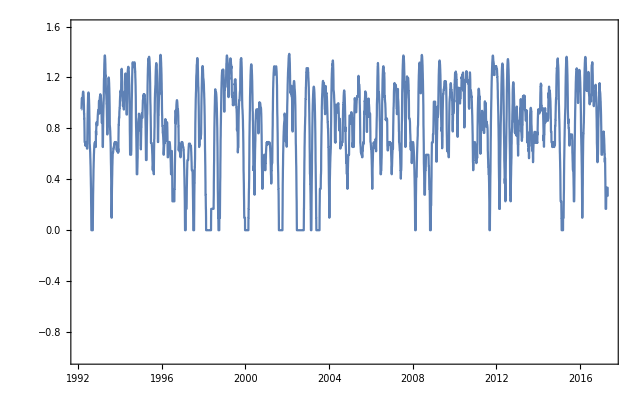

```mathematica
DateListPlot[resultado, PlotRange->{-1,1.6}]
```

```mathematica
Last[parts[[All,1]]]
```

{Day: Wed 15 Feb 2017,3}

```mathematica
Last[parts[[All,2]]]
```

{Day: Fri 17 Feb 2017,3}

```mathematica
parts
```

$Aborted[]

```mathematica
fechas=Drop[database[[1]]["Dates"],-1];
returns1=database[[1]]["Returns"];
```

```mathematica
MovingAverage[returns1,50]
```

```mathematica
Drop[fechas,-1]
```

6464